#### OTOC?

Attempt of Module-wise documentation. 

Here we try some lead-lag analysis on the probability data and see if we can get some order parameter out of it. 

The motivation has been OTOC.

```mathematica
hx=0.01;
ht=0.01;

length = Floor[20/hx];
time =Floor[3/ht];
xi= Array[(#-length/2 -1)*hx&,{length+1}];
ti= Array[(#-1)*ht&,{time+1}];
ProbM=ConstantArray[0,{length+1, time+1}];
```

```mathematica
ST3=ConstantArray[0,{time+1}];
ST5=ConstantArray[0,{time+1}];
ST7=ConstantArray[0,{time+1}];
```

```mathematica
Diff=1;
β=0.5;
k=0.0;
θ=0;
α=10;
xzero=4;
sigma=0.1;
sigma1=0.01;
xs=0;
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.};
AlphaValues={0,.1,.25,0.5,1,2,3,4,5,6,7,8,9,10};
```

```mathematica
BetaValues={1.25,1.5,1.75,2.25,2.5,2.75,3.25,3.5,3.75,4.5,5.5,6.5,7.5,8.5};
AlphaValues={0};
xzerovalues={0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.};
```

```mathematica
For[i=1,i<28,i++,
For[j=1,j<15,j++,

α=AlphaValues[[j]];
β=BetaValues[[i]];
xzero=xzerovalues[[p]];
]
]
```

```mathematica
LaunchKernels[]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
ParallelDo[
Do[
α=0;

A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\PT_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".mat"];


For[j=1,j<length+1,j++,
For[s=1,s<time+1,s++,
ProbM[[j,s]]=A[[1,j,s]]; 
]
];


For[s=1,s<time+1,s++,
ST3[[s]]=hx*Sum[xi[[j]]xi[[j]]xi[[j]]ProbM[[j,s]],{j,length}];
ST5[[s]]=hx*Sum[xi[[j]]xi[[j]]xi[[j]]xi[[j]]xi[[j]]ProbM[[j,s]],{j,length}];
ST7[[s]]=hx*Sum[xi[[j]]xi[[j]]xi[[j]]xi[[j]]xi[[j]]xi[[j]]xi[[j]]ProbM[[j,s]],{j,length}];
];


Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST3_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",ST3];

Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST5_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",ST5];

Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST7_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",ST7];

,{β,BetaValues}]
,{xzero,xzerovalues}]
```

$Aborted

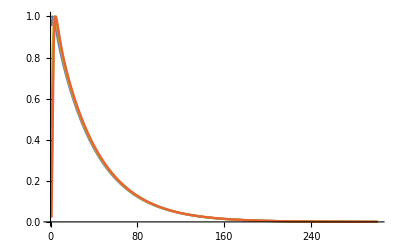

```mathematica
ListLinePlot[{ST1/Max[ST1],ST3/Max[ST3],ST5/Max[ST5],ST7/Max[ST7]}, PlotRange->Full]
```